```mathematica
mxsol= Compile[{β,ω},
h=1;
tm =100;
y[t_]=({{y1[t]}, {y2[t]}});
B = ({{β, ω}, {-ω, β}});
init=y[0]=={{-1},{0}};
sol=NDSolve[N[LogicalExpand[y'[t]==B.y[t-h]&&init]],{y1,y2},{t,0,tm}];
yy1[t_]=y1[t]/.sol[[1]];
yy2[t_]=y2[t]/.sol[[1]];
FindMaximum[{√(yy1[t]^2+yy2[t]^2)&&h≤ t≤ tm},{t,h},Method->"Newton",WorkingPrecision->30][[1]]]
wt = Compile[{β},
th1=0.9999;
dw = 0.001;
Catch[Do[If[mxsol[β,w]>th1,Throw[w]],{w,0,10,dw}]]]
```

CompiledFunction[{β,ω},h=1;tm=100;y[t_]={{y1[t]},{y2[t]}};B={{β,ω},{-ω,β}};init=y[0]=={{-1},{0}};sol=NDSolve[N[LogicalExpand[y'[t]==B.y[t-h]&&init]],{y1,y2},{t,0,tm}];yy1[t_]=y1[t]/.sol⟦1⟧;yy2[t_]=y2[t]/.sol⟦1⟧;FindMaximum[{√(yy1[t]^2+yy2[t]^2)&&h≤t≤tm},{t,h},Method→Newton,WorkingPrecision→30]⟦1⟧,-CompiledCode-]

CompiledFunction[{β},th1=0.9999;dw=0.001;Catch[Do[If[mxsol[β,w]>th1,Throw[w]],{w,0,10,dw}]],-CompiledCode-]

```mathematica
wt[-0.9]
```

0.544

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

CompiledFunction::cfse: Compiled expression {0.9999999988700480901826495,{t→1.666698358965685401085657}} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 9; proceeding with uncompiled evaluation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 15; proceeding with uncompiled evaluation.

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

CompiledFunction::cfse: Compiled expression {0.9999999988700480901826495,{t→1.666698358965685401085657}} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 9; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfex will be suppressed during this calculation.

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of NDSolve::ihist will be suppressed during this calculation.

CompiledFunction::cfse: Compiled expression {0.8999999999455821075855511,{t→1.714293166018898895584806}} should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfse will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-0.04806100330580768903865773} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindMaximum::nrnum: The function value -False is not a real number at {t} = {-0.04806100330580768903865773}.

FindMaximum::nrnum: The function value -False is not a real number at {t} = {0.005064124212578093525434877}.

InterpolatingFunction::dmval: Input value {-0.001081329571471355414102914} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaximum::nrnum: The function value -False is not a real number at {t} = {-0.001081329571471355414102914}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than 25. digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

General::stop: Further output of FindMaximum::fmgz will be suppressed during this calculation.

{{-1.5,0.},{-1.4,0.36},{-1.3,0.38},{-1.2,0.4325},{-1.1,0.4775},{-1.,0.5375},{-0.9,0.545},{-0.8,0.5925},{-0.7,0.575},{-0.6,0.57},{-0.5,0.5525},{-0.4,0.5275},{-0.3,0.485},{-0.2,0.4175},{-0.1,0.305},{0.,0.}}

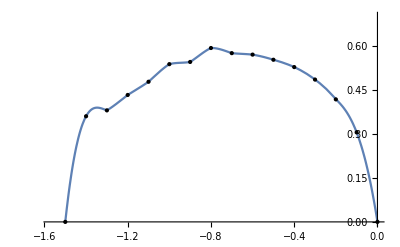

```mathematica
data2 = Table[{β,wt[β]},{β,-1.5,0,0.1}]
ifun = Interpolation[data2];
Plot[{ifun[β]}, {β,-1.5,0}, PlotRange->{{-π/2,0},{0,0.7}},Axes->{True,True}, Epilog->Map[Point,data2]]
```

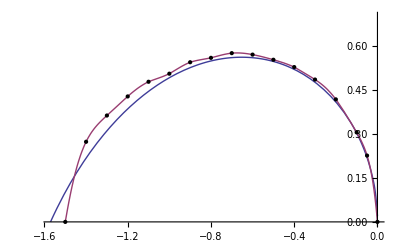

```mathematica
rehl ={{-1.5707963267948966,9.620755706465509*^-17},{-1.5607963267948965,0.015488527363793933},{-1.5507963267948965,0.030553175730054862},{-1.5407963267948965,0.04521488873230396},{-1.5307963267948965,0.059492752594556095},{-1.5207963267948965,0.0734042177388241},{-1.5107963267948965,0.08696528737654338},{-1.5007963267948965,0.10019067890796463},{-1.4907963267948965,0.11309396277624653},{-1.4807963267948965,0.12568768251210824},{-1.4707963267948965,0.13798345899410053},{-1.4607963267948965,0.1499920813904428},{-1.4507963267948965,0.1617235868052344},{-1.4407963267948967,0.17318733029818636},{-1.4307963267948967,0.18439204666283765},{-1.4207963267948966,0.19534590511848587},{-1.4107963267948966,0.2060565578842146},{-1.4007963267948966,0.2165311834505866},{-1.3907963267948966,0.2267765252389351},{-1.3807963267948966,0.23679892623438095},{-1.3707963267948966,0.24660436009249984},{-1.3607963267948966,0.25619845914768524},{-1.3507963267948966,0.2655865396910382},{-1.3407963267948966,0.27477362483496126},{-1.3307963267948966,0.283764465238877},{-1.3207963267948966,0.2925635579342334},{-1.3107963267948965,0.3011751634561308},{-1.3007963267948965,0.3096033214625812},{-1.2907963267948965,0.3178518649998698},{-1.2807963267948965,0.3259244335531223},{-1.2707963267948965,0.33382448500449774},{-1.2607963267948965,0.3415553066069946},{-1.2507963267948965,0.34912002506936496},{-1.2407963267948965,0.3565216158367586},{-1.2307963267948965,0.36376291164225916},{-1.2207963267948965,0.37084661039619504},{-1.2107963267948965,0.3777752824728726},{-1.2007963267948965,0.38455137744801254},{-1.1907963267948964,0.39117723033458535},{-1.1807963267948967,0.39765506735979683},{-1.1707963267948966,0.4039870113216247},{-1.1607963267948966,0.41017508655943713},{-1.1507963267948966,0.4162212235698046},{-1.1407963267948966,0.4221272632955595},{-1.1307963267948966,0.42789496111345027},{-1.1207963267948966,0.4335259905433033},{-1.1107963267948966,0.4390219466994437},{-1.1007963267948966,0.4443843495031727},{-1.0907963267948966,0.4496146466733587},{-1.0807963267948966,0.45471421651062405},{-1.0707963267948966,0.4596843704891898},{-1.0607963267948965,0.46452635566916256},{-1.0507963267948965,0.46924135694088637},{-1.0407963267948965,0.47383049911192754},{-1.0307963267948965,0.47829484884630763},{-1.0207963267948965,0.48263541646472113},{-1.0107963267948965,0.48685315761368375},{-1.0007963267948965,0.4909489748108205},{-0.9907963267948966,0.49492371887283465},{-0.9807963267948966,0.49877819023208175},{-0.9707963267948966,0.5025131401470977},{-0.9607963267948966,0.506129271811902},{-0.9507963267948966,0.5096272413684049},{-0.9407963267948966,0.5130076588257816},{-0.9307963267948965,0.5162710888902501},{-0.9207963267948965,0.5194180517082733},{-0.9107963267948965,0.5224490235258256},{-0.9007963267948965,0.5253644372659897},{-0.8907963267948965,0.5281646830267973},{-0.8807963267948965,0.5308501085008864},{-0.8707963267948965,0.5334210193182134},{-0.8607963267948966,0.5358776793127342},{-0.8507963267948966,0.5382203107136502},{-0.8407963267948966,0.5404490942614913},{-0.8307963267948966,0.5425641692489984},{-0.8207963267948966,0.5445656334864357},{-0.8107963267948965,0.5464535431906498},{-0.8007963267948965,0.5482279127968477},{-0.7907963267948965,0.5498887146917276},{-0.7807963267948965,0.5514358788662391},{-0.7707963267948965,0.5528692924858725},{-0.7607963267948965,0.5541887993759869},{-0.7507963267948965,0.5553941994192705},{-0.7407963267948965,0.5564852478619807},{-0.7307963267948966,0.5574616545251425},{-0.7207963267948966,0.5583230829163696},{-0.7107963267948966,0.5590691492374237},{-0.7007963267948966,0.5596994212820334},{-0.6907963267948966,0.5602134172178362},{-0.6807963267948965,0.5606106042456047},{-0.6707963267948965,0.5608903971281322},{-0.6607963267948965,0.5610521565802975},{-0.6507963267948965,0.5610951875108829},{-0.6407963267948965,0.5610187371056675},{-0.6307963267948965,0.5608219927401613},{-0.6207963267948965,0.5605040797090458},{-0.6107963267948966,0.5600640587579492},{-0.6007963267948966,0.5595009234015661},{-0.5907963267948966,0.5588135970103267},{-0.5807963267948966,0.5580009296457873},{-0.5707963267948966,0.5570616946226233},{-0.5607963267948965,0.5559945847725282},{-0.5507963267948965,0.5547982083823907},{-0.5407963267948965,0.5534710847758137},{-0.5307963267948965,0.5520116395032612},{-0.5207963267948965,0.5504181991018249},{-0.5107963267948965,0.5486889853806882},{-0.5007963267948965,0.5468221091827324},{-0.49079632679489654,0.5448155635662651},{-0.48079632679489653,0.5426672163433973},{-0.4707963267948965,0.5403748019029818},{-0.4607963267948965,0.53793591223605},{-0.45079632679489656,0.5353479870700794},{-0.44079632679489655,0.5326083030049026},{-0.43079632679489654,0.5297139615272353},{-0.42079632679489654,0.5266618757622245},{-0.4107963267948965,0.5234487557985227},{-0.4007963267948965,0.5200710923975035},{-0.3907963267948965,0.5165251388664931},{-0.38079632679489656,0.512806890839243},{-0.37079632679489655,0.5089120636629946},{-0.36079632679489654,0.5048360670387115},{-0.35079632679489653,0.5005739764972953},{-0.3407963267948965,0.49612050121715523},{-0.3307963267948965,0.4914699475939756},{-0.32079632679489656,0.48661617785747446},{-0.31079632679489655,0.4815525628866677},{-0.30079632679489654,0.47627192819713593},{-0.29079632679489653,0.47076649185117253},{-0.2807963267948965,0.4650277927613494},{-0.2707963267948965,0.4590466075023679},{-0.2607963267948965,0.452812853291259},{-0.25079632679489655,0.4463154742094767},{-0.24079632679489654,0.4395423069771791},{-0.23079632679489653,0.43247992158703974},{-0.22079632679489652,0.4251134307731269},{-0.21079632679489652,0.41742626050178083},{-0.20079632679489653,0.40939987123967225},{-0.19079632679489653,0.40101341640372334},{-0.18079632679489652,0.39224331971347626},{-0.17079632679489654,0.3830627465127004},{-0.16079632679489653,0.37344093450771654},{-0.15079632679489652,0.36334233519035836},{-0.14079632679489654,0.35272549585449225},{-0.13079632679489653,0.3415415791519796},{-0.12079632679489653,0.32973236485190077},{-0.11079632679489652,0.31722749292238794},{-0.10079632679489653,0.30394056199277636},{-0.09079632679489652,0.28976344084034444},{-0.08079632679489653,0.2745576746100078},{-0.07079632679489653,0.2581409309064587},{-0.06079632679489653,0.24026445159190918},{-0.050796326794896526,0.2205729021612645},{-0.040796326794896524,0.19852614202054883},{-0.030796326794896526,0.1732263726755596},{-0.020796326794896527,0.14295575750720493},{-0.010796326794896526,0.10343719133295229},{-0.0007963267948965253,0.02820989847162101}};
rehlfun = Interpolation[rehl];
data2c = {{-1.5,0.},{-1.4,0.273},{-1.3,0.3625},{-1.2,0.4275},{-1.1,0.47750000000000004},{-1.,0.505},{-0.8999999999999999,0.544},{-0.8,0.559},{-0.7,0.5750000000000001},{-0.6,0.5700000000000001},{-0.5,0.5525},{-0.3999999999999999,0.5275},{-0.2999999999999998,0.485},{-0.19999999999999996,0.4175},{-0.09999999999999987,0.305},{-0.05,0.226},{0.,0.}};
ifunc = Interpolation[data2c,InterpolationOrder->8];

Plot[{rehlfun[β],ifunc[β]}, {β,-π/2,0}, PlotRange->{{-π/2,0},{0,0.7}},Axes->{True,True}, Epilog->Map[Point,data2c]]
```

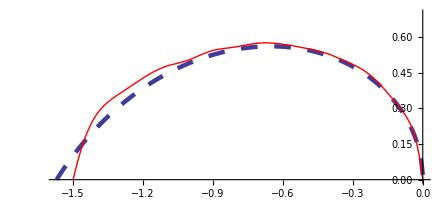

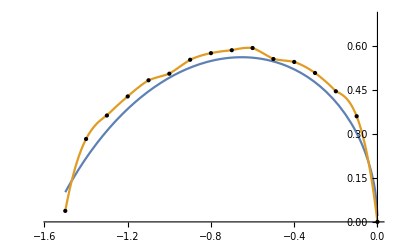

```mathematica
Plot[{rehlfun[β], ifunc[β]}, {β,-π/2,0}, PlotRange->{{-π/2,0},{0,0.7}},PlotStyle ->{Directive[Thickness[0.008],Dashing[0.03]], Directive[Red]}, Axes->{True,True},AspectRatio->Automatic,AxesStyle->Directive[FontSize->16,FontFamily->"TimesNewRoman"]]
```

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of NDSolve::ihist will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

{{-1.5,0.},{-1.495,0.0825},{-1.49,0.1175},{-1.485,0.145},{-1.48,0.165},{-1.475,0.185},{-1.47,0.2025},{-1.465,0.2175},{-1.46,0.2325},{-1.455,0.2475},{-1.45,0.26},{-1.445,0.2725},{-1.44,0.2825},{-1.435,0.295},{-1.43,0.305},{-1.425,0.315},{-1.42,0.325},{-1.415,0.335},{-1.41,0.3425},{-1.405,0.3525},{-1.4,0.36}}

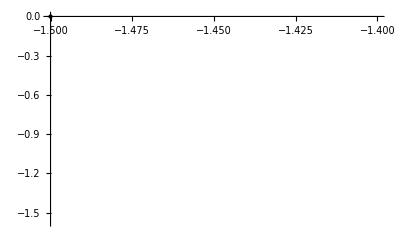

```mathematica
rehl ={{-1.5707963267948966,9.620755706465509*^-17},{-1.5607963267948965,0.015488527363793933},{-1.5507963267948965,0.030553175730054862},{-1.5407963267948965,0.04521488873230396},{-1.5307963267948965,0.059492752594556095},{-1.5207963267948965,0.0734042177388241},{-1.5107963267948965,0.08696528737654338},{-1.5007963267948965,0.10019067890796463},{-1.4907963267948965,0.11309396277624653},{-1.4807963267948965,0.12568768251210824},{-1.4707963267948965,0.13798345899410053},{-1.4607963267948965,0.1499920813904428},{-1.4507963267948965,0.1617235868052344},{-1.4407963267948967,0.17318733029818636},{-1.4307963267948967,0.18439204666283765},{-1.4207963267948966,0.19534590511848587},{-1.4107963267948966,0.2060565578842146},{-1.4007963267948966,0.2165311834505866},{-1.3907963267948966,0.2267765252389351},{-1.3807963267948966,0.23679892623438095},{-1.3707963267948966,0.24660436009249984},{-1.3607963267948966,0.25619845914768524},{-1.3507963267948966,0.2655865396910382},{-1.3407963267948966,0.27477362483496126},{-1.3307963267948966,0.283764465238877},{-1.3207963267948966,0.2925635579342334},{-1.3107963267948965,0.3011751634561308},{-1.3007963267948965,0.3096033214625812},{-1.2907963267948965,0.3178518649998698},{-1.2807963267948965,0.3259244335531223},{-1.2707963267948965,0.33382448500449774},{-1.2607963267948965,0.3415553066069946},{-1.2507963267948965,0.34912002506936496},{-1.2407963267948965,0.3565216158367586},{-1.2307963267948965,0.36376291164225916},{-1.2207963267948965,0.37084661039619504},{-1.2107963267948965,0.3777752824728726},{-1.2007963267948965,0.38455137744801254},{-1.1907963267948964,0.39117723033458535},{-1.1807963267948967,0.39765506735979683},{-1.1707963267948966,0.4039870113216247},{-1.1607963267948966,0.41017508655943713},{-1.1507963267948966,0.4162212235698046},{-1.1407963267948966,0.4221272632955595},{-1.1307963267948966,0.42789496111345027},{-1.1207963267948966,0.4335259905433033},{-1.1107963267948966,0.4390219466994437},{-1.1007963267948966,0.4443843495031727},{-1.0907963267948966,0.4496146466733587},{-1.0807963267948966,0.45471421651062405},{-1.0707963267948966,0.4596843704891898},{-1.0607963267948965,0.46452635566916256},{-1.0507963267948965,0.46924135694088637},{-1.0407963267948965,0.47383049911192754},{-1.0307963267948965,0.47829484884630763},{-1.0207963267948965,0.48263541646472113},{-1.0107963267948965,0.48685315761368375},{-1.0007963267948965,0.4909489748108205},{-0.9907963267948966,0.49492371887283465},{-0.9807963267948966,0.49877819023208175},{-0.9707963267948966,0.5025131401470977},{-0.9607963267948966,0.506129271811902},{-0.9507963267948966,0.5096272413684049},{-0.9407963267948966,0.5130076588257816},{-0.9307963267948965,0.5162710888902501},{-0.9207963267948965,0.5194180517082733},{-0.9107963267948965,0.5224490235258256},{-0.9007963267948965,0.5253644372659897},{-0.8907963267948965,0.5281646830267973},{-0.8807963267948965,0.5308501085008864},{-0.8707963267948965,0.5334210193182134},{-0.8607963267948966,0.5358776793127342},{-0.8507963267948966,0.5382203107136502},{-0.8407963267948966,0.5404490942614913},{-0.8307963267948966,0.5425641692489984},{-0.8207963267948966,0.5445656334864357},{-0.8107963267948965,0.5464535431906498},{-0.8007963267948965,0.5482279127968477},{-0.7907963267948965,0.5498887146917276},{-0.7807963267948965,0.5514358788662391},{-0.7707963267948965,0.5528692924858725},{-0.7607963267948965,0.5541887993759869},{-0.7507963267948965,0.5553941994192705},{-0.7407963267948965,0.5564852478619807},{-0.7307963267948966,0.5574616545251425},{-0.7207963267948966,0.5583230829163696},{-0.7107963267948966,0.5590691492374237},{-0.7007963267948966,0.5596994212820334},{-0.6907963267948966,0.5602134172178362},{-0.6807963267948965,0.5606106042456047},{-0.6707963267948965,0.5608903971281322},{-0.6607963267948965,0.5610521565802975},{-0.6507963267948965,0.5610951875108829},{-0.6407963267948965,0.5610187371056675},{-0.6307963267948965,0.5608219927401613},{-0.6207963267948965,0.5605040797090458},{-0.6107963267948966,0.5600640587579492},{-0.6007963267948966,0.5595009234015661},{-0.5907963267948966,0.5588135970103267},{-0.5807963267948966,0.5580009296457873},{-0.5707963267948966,0.5570616946226233},{-0.5607963267948965,0.5559945847725282},{-0.5507963267948965,0.5547982083823907},{-0.5407963267948965,0.5534710847758137},{-0.5307963267948965,0.5520116395032612},{-0.5207963267948965,0.5504181991018249},{-0.5107963267948965,0.5486889853806882},{-0.5007963267948965,0.5468221091827324},{-0.49079632679489654,0.5448155635662651},{-0.48079632679489653,0.5426672163433973},{-0.4707963267948965,0.5403748019029818},{-0.4607963267948965,0.53793591223605},{-0.45079632679489656,0.5353479870700794},{-0.44079632679489655,0.5326083030049026},{-0.43079632679489654,0.5297139615272353},{-0.42079632679489654,0.5266618757622245},{-0.4107963267948965,0.5234487557985227},{-0.4007963267948965,0.5200710923975035},{-0.3907963267948965,0.5165251388664931},{-0.38079632679489656,0.512806890839243},{-0.37079632679489655,0.5089120636629946},{-0.36079632679489654,0.5048360670387115},{-0.35079632679489653,0.5005739764972953},{-0.3407963267948965,0.49612050121715523},{-0.3307963267948965,0.4914699475939756},{-0.32079632679489656,0.48661617785747446},{-0.31079632679489655,0.4815525628866677},{-0.30079632679489654,0.47627192819713593},{-0.29079632679489653,0.47076649185117253},{-0.2807963267948965,0.4650277927613494},{-0.2707963267948965,0.4590466075023679},{-0.2607963267948965,0.452812853291259},{-0.25079632679489655,0.4463154742094767},{-0.24079632679489654,0.4395423069771791},{-0.23079632679489653,0.43247992158703974},{-0.22079632679489652,0.4251134307731269},{-0.21079632679489652,0.41742626050178083},{-0.20079632679489653,0.40939987123967225},{-0.19079632679489653,0.40101341640372334},{-0.18079632679489652,0.39224331971347626},{-0.17079632679489654,0.3830627465127004},{-0.16079632679489653,0.37344093450771654},{-0.15079632679489652,0.36334233519035836},{-0.14079632679489654,0.35272549585449225},{-0.13079632679489653,0.3415415791519796},{-0.12079632679489653,0.32973236485190077},{-0.11079632679489652,0.31722749292238794},{-0.10079632679489653,0.30394056199277636},{-0.09079632679489652,0.28976344084034444},{-0.08079632679489653,0.2745576746100078},{-0.07079632679489653,0.2581409309064587},{-0.06079632679489653,0.24026445159190918},{-0.050796326794896526,0.2205729021612645},{-0.040796326794896524,0.19852614202054883},{-0.030796326794896526,0.1732263726755596},{-0.020796326794896527,0.14295575750720493},{-0.010796326794896526,0.10343719133295229},{-0.0007963267948965253,0.02820989847162101}};
rehlfun = Interpolation[rehl];
data3 = Table[{β,wt[β]},{β,-1.5,-1.4,0.005}]
ifun3 = Interpolation[data3];
Plot[{rehlfun[β],ifun3[β]}, {β,-1.5,-1.4}, PlotRange->{{-π/2,0}},Axes->{True,True}, Epilog->Map[Point,data3]]
```

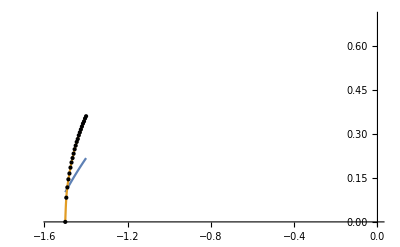

```mathematica
Plot[{rehlfun[β],ifun3[β]}, {β,-1.5,-1.4}, PlotRange->{{-π/2,0},{0,0.7}},Axes->{True,True}, Epilog->Map[Point,data3]]
```

InterpolatingFunction::dmval: Input value {-1.57079} lies outside the range of data in the interpolating function. Extrapolation will be used.

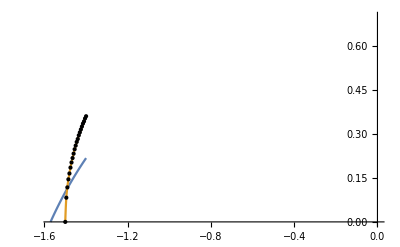

```mathematica
Plot[{rehlfun[β],ifun3[β]}, {β,-π/2,-1.4}, PlotRange->{{-π/2,0},{0,0.7}},Axes->{True,True}, Epilog->Map[Point,data3]]
```